# Wolfram Workshop

## Capítulo 1

## 1. Ingreso de entradas y operaciones básicas

En Wolfram, puedes realizar cálculos simples y complejos.

```mathematica
2+2
```

4

```mathematica
5*3-7.5
```

7.5

```mathematica
(5-3)^(1+2)
```

8

```mathematica
((5-3)^(1+2))/4
```

2

```mathematica
(5-3)^(1+2)/4
```

2

## 2. Funciones incorporadas

Wolfram Language tiene miles de funciones incorporadas.

Máximo común divisor (GCD)

```mathematica
GCD[12,15]
```

3

Gráfico de una función seno

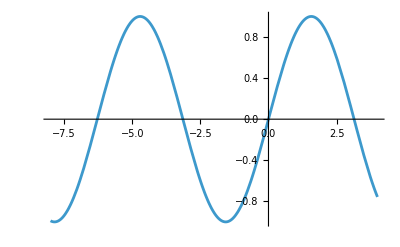

```mathematica
Plot[Sin[x],{x,-8,4}]
```

## 3. Listas y operaciones con listas

Las listas son colecciones ordenadas de elementos. Pueden contener números, variables, cálculos u otras listas.

Máximo común divisor (GCD)

```mathematica
{1,2,3}
```

{1,2,3}

Operaciones con listas

```mathematica
{1,2,3}+2
```

{3,4,5}

Extracción de elementos de una lista

```mathematica
{a,b,c,d}[[3]]
```

c

Creación de una lista con Range

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

## 4. Fracciones y decimales

Wolfram Language maneja fracciones y decimales de manera precisa.

Fracciones exactas

```mathematica
4/3
```

4/3

Simplificación de fracciones con Together

```mathematica
Together[1/a+1/b]
```

(a+b)/(a b)

```mathematica
1/x+1/(x+1)+1/(x+2)+1/(x+3)
```

1/x+1/(1+x)+1/(2+x)+1/(3+x)

```mathematica
Together[1/x+1/(x+1)+1/(x+2)+1/(x+3)]
```

(2 (3+11 x+9 x^2+2 x^3))/(x (1+x) (2+x) (3+x))

Conversión a decimales con N

```mathematica
N[4/3]
```

1.33333

Notación científica

```mathematica
ScientificForm[0.00123]
```

1.23×10^-3

## 5. Variables y funciones

Puedes definir variables y funciones personalizadas en Wolfram Language.

Asignación de variables

```mathematica
x=2
1+2x
```

2

5

Borrado de variables

```mathematica
Clear[x]
1+2x
```

1+2 x

```mathematica
x
```

x

Definición de funciones

```mathematica
f[x_]:=1+2x
```

```mathematica
f[x]
f[2]
```

1+2 x

5

Sustitución en expresiones (/.)

```mathematica
1+2x/. x->2
```

5

```mathematica
x^2+7/. x->2
```

11

## ejercicios

### 1. Calcula el resultado de la siguiente expresión:

(3+5)(2-4)^2

```mathematica
(3+5)(2-4)^2
```

32

### 2. Crea una lista con los números del 1 al 20 y luego suma 5 a cada elemento de la lista.

```mathematica
Range[20]+5
```

{6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

### 3. Define una función que calcule el cuadrado de un número y luego aplícala al número 7.

```mathematica
f[x_]:=x^2
f[7]
```

49

### 4. Grafica la función coseno desde -10 hasta 10.

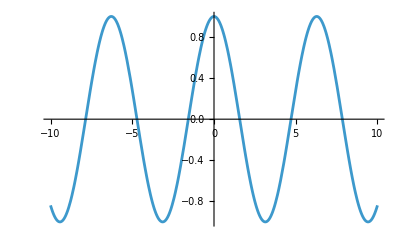

```mathematica
Plot[Cos[x], {x,-10,10}]
```

### 5. Calcula el máximo común divisor (GCD) de 24 y 36.

```mathematica
GCD[24,36]
```

12

## Capítulo 2

## 2.1. Álgebra

Wolfram Language es muy potente para manipular expresiones algebraicas, resolver ecuaciones y trabajar con polinomios.

Factorización de expresiones

```mathematica
Factor[x^2+2x+1]
```

(1+x)^2

Resolución de ecuaciones

```mathematica
Solve[x^2+5x-6==0,x]
```

{{x→-6},{x→1}}

Resolución de sistemas de ecuaciones

```mathematica
Solve[{x^2+5==y,7x-5==y},{x,y}]
```

{{x→2,y→9},{x→5,y→30}}

Uso de Reduce para inecuaciones

```mathematica
Reduce[(x-1)(x-2)(x-3)(x-4)>0,x]
```

x<1||2<x<3||x>4

Visualización de inecuaciones con NumberLinePlot

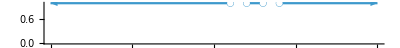

```mathematica
NumberLinePlot[x<1||2<x<3||x>4,{x,-10,10}]
```

## 2.2. Gráficos en 2D

Wolfram Language permite crear gráficos en 2D de funciones, regiones y más.

Gráfico de una función polinómica

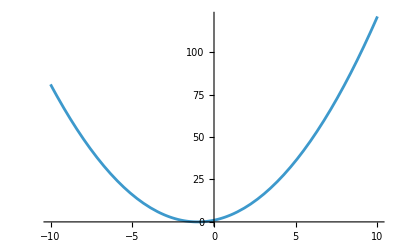

```mathematica
Plot[x^2+2x+1,{x,-10,10}]
```

Gráfico de una región definida por inecuaciones

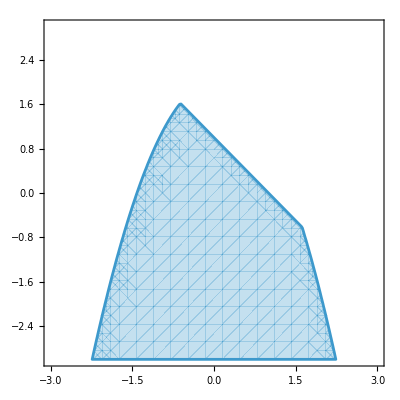

```mathematica
RegionPlot[x^2+y<2&&x+y<1,{x,-3,3},{y,-3,3}]
```

Personalización de gráficos con leyendas

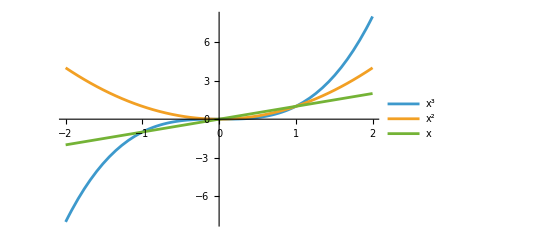

```mathematica
Plot[{x^3,x^2,x},{x,-2,2},PlotLegends->"Expressions"]
```

Rellenar el área bajo una curva

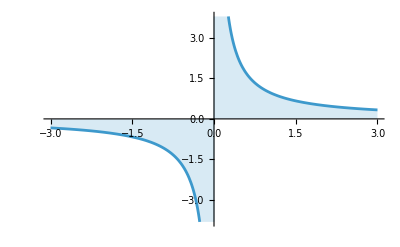

```mathematica
Plot[1/x,{x,-3,3},Filling->Axis]
```

Combinación de gráficos con Show

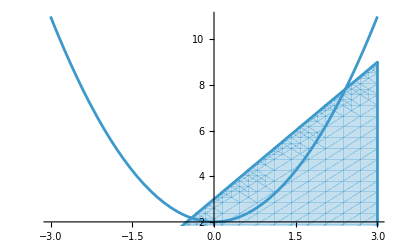

```mathematica
Show[{Plot[x^2+2,{x,-3,3}],RegionPlot[2x>y-3,{x,-3,3},{y,0,9}]}]
```

## 2.3. Geometría

Wolfram Language permite trabajar con formas geométricas en 2D y 3D, calcular áreas, volúmenes y más.

Creación de un círculo



```mathematica
Graphics[Disk[]]
```

```mathematica
Graphics[Disk[{0,0},1]]
```

-Graphics-

Creación de un rectángulo

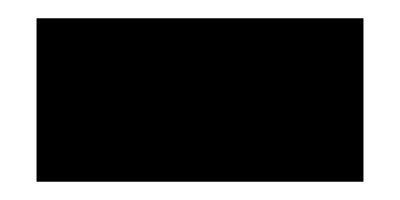

```mathematica
Graphics[Rectangle[{0,0},{4,2}]]
```

Combinación de formas con estilos

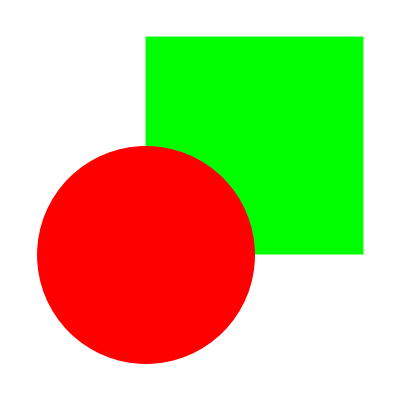

```mathematica
Graphics[{
Green,Rectangle[{0,0},{2,2}],
Red,Disk[]}]
```

Cálculo del área de un triángulo

```mathematica
base=2
h=5
(base×h)/2
```

2

5

5

```mathematica
tr=SASTriangle[1,90°,2]
Area[tr]
```

Triangle[{{0,0},{√5,0},{4/(√5),2/(√5)}}]

1

Visualización de objetos en 3D

```mathematica
Graphics3D[Ball[]]
```

-Graphics3D-

Cálculo del volumen

```mathematica
Volume[Ball[]]
```

(4 π)/3

## 2.4. Trigonometría

Identidades trigonométricas

```mathematica
Sin[x]/Cos[x]==Tan[x]
```

True

Funciones trigonométricas inversas

```mathematica
ArcTan[1]
```

π/4

Expansión de expresiones trigonométricas

```mathematica
TrigExpand[Sin[2x]]
```

2 Cos[x] Sin[x]

Resolución de ecuaciones trigonométricas

```mathematica
Solve[Cos[x]^2+Sin[x]^2==x]
```

{{x→1}}

## 2.5. Coordenadas polares

Gráfico polar

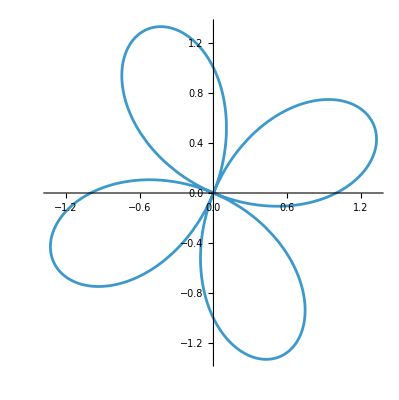

```mathematica
PolarPlot[Sin[2θ]+Cos[2θ],{θ,0,2π}]
```

Conversión de coordenadas cartesianas a polares

```mathematica
ToPolarCoordinates[{1,1}]
```

{√2,π/4}

## 2.6. Funciones exponenciales y logarítmicas

Logaritmo natural

```mathematica
Log[E^2]
```

2

Logaritmo en base 2

```mathematica
Log[2,64]
```

6

Gráfico en escala logarítmica

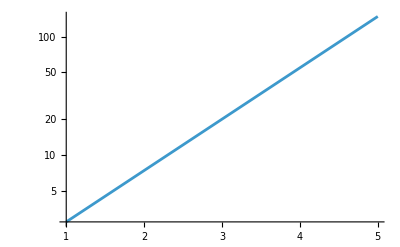

```mathematica
LogPlot[E^x,{x,1,5}]
```

Gráfico con ambos ejes logarítmicos

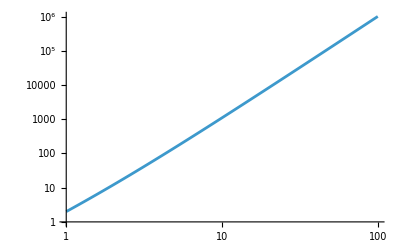

```mathematica
LogLogPlot[x^2+x^3,{x,1,100}]
```

## ejercicios

### 1. Factoriza la expresión

x^3+6 x^2+11x-6

```mathematica
Factor[x^3-6 x^2+11x-6]
```

(-3+x) (-2+x) (-1+x)

### 2. Resuelve el sistema de ecuaciones

{x+y=5
x-y=1

```mathematica
Solve[{x+y==5x-y==1},{x,y}]
```

{{x→1/3,y→2/3}}

### 3. Grafica la función:

y=sin(x)+cos(x),  x∈[0,2π]

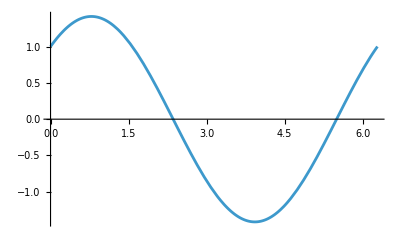

```mathematica
Plot[Sin[x]+Cos[x],{x,0,2π}]
```

### 4. Calcula el área de un círculo con radio 5.

```mathematica
Area[Disk[{0,0},5]]
```

25 π

### 5. Resuelve la ecuación trigonométrica

sin(x)=cos(x),  x∈(0,2π)

```mathematica
Solve[{Sin[x]==Cos[x],0<x<2π},x]
```

{{x→-2 ArcTan[1-√2]},{x→2 π-2 ArcTan[1+√2]}}

## Capítulo 3

límites, derivadas, integrales, secuencias, sumas y series

## 3.1. Límites

Calculo de límites de funciones, tanto en puntos finitos como en el infinito

Cálculo de un límite en un punto

```mathematica
Limit[(x^3-1)/(x-1),x->1]
```

3

```mathematica
lim_(x->1) (x^3-1)/(x-1)
```

3

Cálculo de un límite en el infinito

```mathematica
Limit[(2x^3-1)/(5x^3+x-1),x->Infinity]
```

2/5

```mathematica
Limit[(2 x^3-1)/(5 x^3+x-1),x->∞]
```

2/5

```mathematica
lim_(x->∞) (2 x^3-1)/(5 x^3+x-1)
```

2/5

Límites laterales

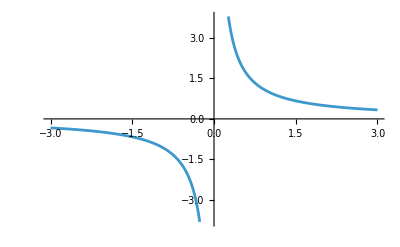

```mathematica
Plot[1/x,{x,-3,3}]
```

```mathematica
lim_(x->0) 1/x
```

Indeterminate

```mathematica
lim_(x->0^-) 1/x
```

-∞

```mathematica
Limit[1/x,x->0,Direction->1]  (*Límite por la izquierda*)
```

-∞

```mathematica
Limit[1/x,x->0,Direction->-1]  (*Límite por la derecha*)
```

∞

```mathematica
lim_(x->0^+) 1/x
```

∞

Limites por arriba/abajo

(|x|)/x,  x∈ℝ

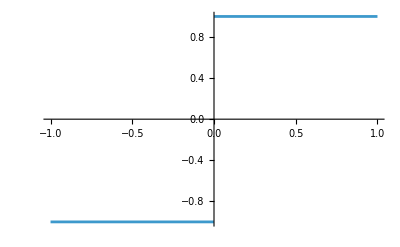

```mathematica
Plot[Abs[x]/x,{x,-1,1}]
```

```mathematica
Limit[Abs[x]/x,x->0,Direction->"FromAbove"]
```

1

```mathematica
Limit[Abs[x]/x,x->0,Direction->"FromBelow"]
```

-1

## 3.2. Derivadas

Derivada de una función

```mathematica
D[x^6,x]
```

6 x^5

Derivada de una función trigonométrica

```mathematica
Sin'[x]
D[Sin[x],x]
```

Cos[x]

Cos[x]

Derivada de una función definida

```mathematica
f[x_]:=x^2+2x+1
f[x]
```

1+2 x+x^2

```mathematica
f'[x]
D[f[x],x]
```

2+2 x

2+2 x

Gráfico de una función y su derivada

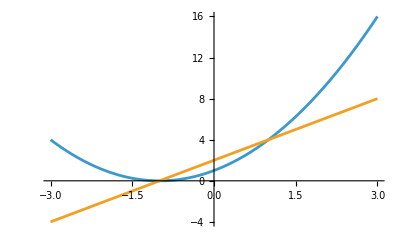

```mathematica
Plot[{f[x],f'[x]},{x,-3,3}]
```

Derivadas de orden superior

```mathematica
D[x^6,{x,3}]
```

120 x^3

## 3.3. Integrales

Calculo de integrales, tanto definidas como indefinidas

Integral indefinida

```mathematica
Integrate[8 x^4,x]
```

(8 x^5)/5

```mathematica
∫8 x^4 ⅆx
```

(8 x^5)/5

Integral definida

```mathematica
Integrate[Sin[x],{x,0,Pi}]
```

2

```mathematica
∫_0^π Sin[x]ⅆx
```

2

Aproximación numérica de una integral

```mathematica
∫_0^π (x^3 Sin[x]+2 Log[3x]^2)ⅆx
```

π (-6+π^2+2 (2+Log[3]^2+Log[9] (-1+Log[π])+(-2+Log[π]) Log[π]))

```mathematica
NIntegrate[x^3 Sin[x]+2 Log[3x]^2,{x,0,Pi}]
```

28.1531

## 3.4. Secuencias, sumas y series

Generación de una secuencia

```mathematica
Table[x^2,{x,1,7}]
```

{1,4,9,16,25,36,49}

Secuencia de Fibonacci

```mathematica
Table[Fibonacci[x],{x,1,7}]
```

{1,1,2,3,5,8,13}

Secuencia recursiva

```mathematica
RecurrenceTable[{
a[x]==2 a[x-1],
a[1]==1},
a,
{x,1,8}]
```

{1,2,4,8,16,32,64,128}

Función de generación para una secuencia

```mathematica
FindSequenceFunction[{2,4,6,8},n]
```

2 n

Suma de una secuencia

```mathematica
Sum[i (i+1),{i,1,10}]
```

440

```mathematica
∑_(i=1)^10 i(i+1)
```

440

```mathematica
∑_(i=1)^n ∑_(j=1)^n i j
```

1/4 n^2 (1+n)^2

Serie de potencias (aproximaciones)

e^(x^2)

```mathematica
Series[E^(x^2),{x,0,8}]
```

1+x^2+x^4/2+x^6/6+x^8/24+O[x]^9

Truncamiento de una serie

```mathematica
Normal[Series[E^(x^2),{x,0,8}]]
```

1+x^2+x^4/2+x^6/6+x^8/24

## Representación gráfica

Ecuaciones paramétricas.

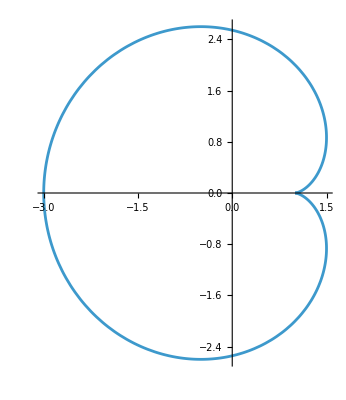

```mathematica
ParametricPlot[{2 Cos[t]-Cos[2 t],2 Sin[t]-Sin[2 t]},{t,0,2 Pi}]
```

```mathematica
Plot3D[Sin[x] Sin[y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

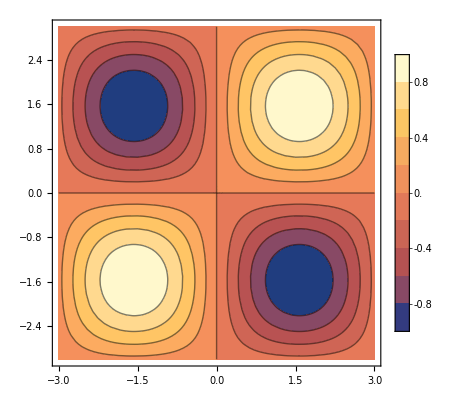

```mathematica
ContourPlot[Sin[x] Sin[y],{x,-3,3},{y,-3,3},PlotLegends->Automatic]
```

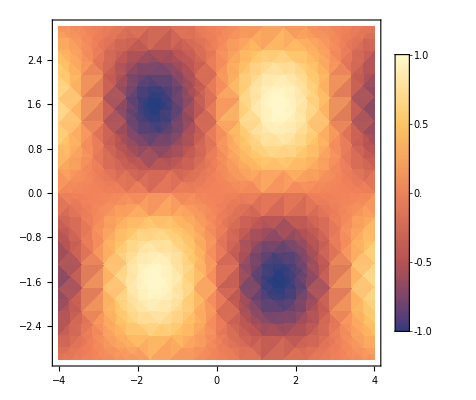

```mathematica
DensityPlot[Sin[x] Sin[y],{x,-4,4},{y,-3,3},PlotLegends->Automatic]
```

## ejercicios

### 1. Calcula el límite de la siguiente función cuando x tiende a 0:

f(x)=(sin(x))/x

lim_(x→0) (sin(x))/x

```mathematica
lim_(x->0) Sin[x]/x
```

1

### 2. Calcula la derivada de la función:

f(x)=e^(x^2)

```mathematica
D[E^(x^2),x]
```

2 ⅇ^(x^2) x

### 3. Calcula la integral definida de la función:

f(x)=∫_0^1 x^3 ⅆx

```mathematica
Integrate[x^3,x]
```

x^4/4

```mathematica
∫_0^1 x^3 ⅆx
```

1/4

### 4. Genera una secuencia de los primeros 10 números cuadrados y calcula su suma.

```mathematica
Table[i^2,{i,1,10}]
Total[%]
```

{1,4,9,16,25,36,49,64,81,100}

385

```mathematica
∑_(i=1)^10 i^2
```

385

### 5. Encuentra la serie de potencias de la función:

f(x)=cos(x)

al rededor de x=0, hasta el orden 6.

```mathematica
Series[Cos[x],{x,0,6}]
```

1-x^2/2+x^4/24-x^6/720+O[x]^7

## Capítulo 4

## 4.1. Gráficos en 3D

Gráfico de una superficie en 3D

```mathematica
Plot3D[x^2-y^2,{x,-3,3},{y,-3,3}]
```

-Graphics3D-

```mathematica
Plot3D[{x^2+y^2,-(x^2+y^2)},{x,-2,2},{y,-2,2},PlotLegends->Automatic]
```

-Graphics3D-

Gráfico de una curva paramétrica en 3D

```mathematica
ParametricPlot3D[{Sin[u],Cos[u],u/10},{u,0,20}]
```

-Graphics3D-

Gráfico en coordenadas esféricas

```mathematica
SphericalPlot3D[Sin[θ],{θ,0,Pi},{φ,0,2 Pi}]
```

-Graphics3D-

Superficie de revolución

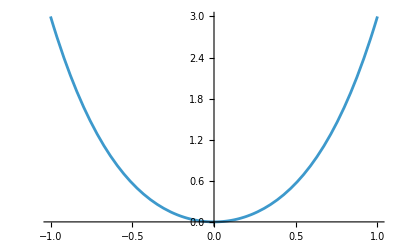

```mathematica
Plot[x^4+2 x^2,{x,-1,1}]
```

```mathematica
RevolutionPlot3D[x^4+2 x^2,{x,-1,1}]
```

-Graphics3D-

## 4.2. Cálculo multivariable

Calculo de derivadas parciales, integrales múltiples y trabajar con funciones de varias variables.

Derivada parcial

```mathematica
D[x^3 z+2 y^2 x+y z^3,y,z]
```

3 z^2

```mathematica
D[(x^3 z+2 y^2 x+y z^3), y,z]
```

3 z^2

```mathematica
D[x^2-2x y+x y z,x,y]
```

-2+z

```mathematica
D[(x^2-2x y+x y z), x,y]
```

-2+z

Integral múltiple

```mathematica
Integrate[Integrate[Integrate[x^2+y^2+z^2,x],y],z]
```

1/3 x^3 y z+1/3 x y^3 z+1/3 x y z^3

```mathematica
∫∫∫(x^2+y^2+z^2)ⅆxⅆyⅆz
```

1/3 x^3 y z+1/3 x y^3 z+1/3 x y z^3

Aproximación numérica de una integral múltiple

```mathematica
∫_-1^1 ∫_-2^x (x Sin[y^2]+y Cos[x^2])ⅆyⅆx
```

1/4 (2 Cos[1]+√(2 π) (-9 FresnelC[√(2/π)]+FresnelS[√(2/π)])+2 Sin[1])

```mathematica
NIntegrate[x Sin[y^2]+y Cos[x^2],{x,-1,1},{y,-2,x}]
```

-3.22434

## 4.3. Análisis y visualización de vectores

Vectores, calculo de productos escalares y vectoriales, visualización de campos vectoriales.

Producto escalar

```mathematica
{1,2,3}.{a,b,c}
```

a+2 b+3 c

```mathematica
Dot[{1,2,3},{a,b,c}]
```

a+2 b+3 c

Producto vectorial

```mathematica
Cross[{1,2,3},{a,b,c}]
```

{-3 b+2 c,3 a-c,-2 a+b}

Producto elemento a elemento

```mathematica
{1,2,3}*{a,b,c}
```

{a,2 b,3 c}

Norma de un vector

∥𝑣∥=√(𝑣_1^2+𝑣_2^2+...+𝑣_n^2)

```mathematica
Norm[{1,1,1}]
```

√3

```mathematica
Norm[{1,2,c}]
```

√(5+Abs[c]^2)

Proyección de un vector

Proy_b(a)=((a•b)/(||b(||)^2))b

```mathematica
a={8,6,7};
b={1,0,0};
```

```mathematica
proy[a_,b_]:=Dot[a,b]/Norm[b]^2*b
```

```mathematica
proy[a,b]
```

{8,0,0}

```mathematica
Projection[a,b]
```

{8,0,0}

Ángulo entre dos vectores

```mathematica
VectorAngle[{1,0},{0,1}]
```

π/2

Gradiente de una función

```mathematica
Grad[x^2+y,{x,y}]
```

{2 x,1}

```mathematica
∇_{x,y} {x^2+y}
```

{{2 x,1}}

```mathematica
∇_{x,y} {x^2+y,x+y^2}
```

{{2 x,1},{1,2 y}}

Divergencia (rotacional) de un campo vectorial

```mathematica
Clear[{f,g,h}]
```

```mathematica
Div[{f[x,y,z],g[x,y,z],h[x,y,z]},{x,y,z}]
```

h^(0,0,1)[x,y,z]+g^(0,1,0)[x,y,z]+f^(1,0,0)[x,y,z]

Visualización de campos vectoriales

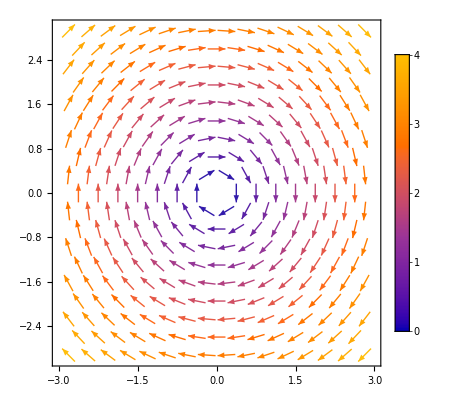

```mathematica
VectorPlot[{y,-x},{x,-3,3},{y,-3,3},PlotLegends->Automatic]
```

```mathematica
VectorPlot3D[{y,-x,z},{x,-3,3},{y,-3,3},{z,-3,3},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
SliceVectorPlot3D[{y,-x,z},{x,-3,3},{y,-3,3},{z,-3,3},PlotLegends->Automatic]
```

-Graphics3D-

## 4.4. Ecuaciones diferenciales

Solución para ecuaciones diferenciales ordinarias (EDO), parciales (EDP) y de retraso (EDR).

Solución general de una EDO

```mathematica
DSolveValue[
y'[x]+y[x]==x,
y[x]
,x]
```

-1+x+ⅇ^-x C[1]

```mathematica
DSolve[
y'[x]+y[x]==x]
```

{{y[x]→-1+x+ⅇ^-x C[1]}}

Las constantes C[n]=C[n] se pueden reemplazar con /. C[n]->value

```mathematica
DSolveValue[y'[x]+y[x]==x,y[x],x] /. C[1]->6
```

-1+6 ⅇ^-x+x

```mathematica
DSolve[y'[x]+y[x]==x] /. C[1]->6
```

{{y[x]→-1+6 ⅇ^-x+x}}

Solución específica de una EDO (IVP)

```mathematica
DSolveValue[{
y'[x]+y[x]==x,
y[0]==-1
},y[x],x]
```

-1+x

```mathematica
DSolve[{
y'[x]+y[x]==x,
y[0]==-1
}]
```

{{y[x]→-1+x}}

Solución numérica de una EDO

```mathematica
sol =NDSolveValue[{
y'[x]==Cos[x^2],
y[0]==0
},y[x],{x,-5,5}]
```

InterpolatingFunction[…][x]

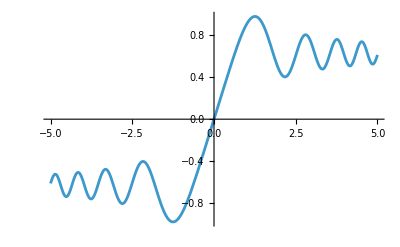

```mathematica
Plot[sol,{x,-5,5}]
```

```mathematica
sol=NDSolve[{
y'[x]==Cos[x^2],
y[0]==0
},y[x],{x,-5,5}]
```

{{y[x]→InterpolatingFunction[…][x]}}

Solución de un sistema de EDOs

```mathematica
{xsol,ysol}=NDSolveValue[{
x'[t]==-y[t]-x[t]^2,
y'[t]==2 x[t]-y[t]^3,
x[0]==1,y[0]==1}
,{x,y},{t,0,20}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

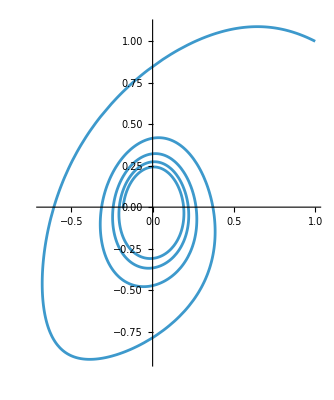

```mathematica
ParametricPlot[{xsol[t],ysol[t]},{t,0,20}]
```

## 4.5 . Análisis complejo

Números complejos, calculo de conjugados, partes reales e imaginarias, y conversión entre formas exponenciales y trigonométricas.

Operaciones con números complejos

```mathematica
ⅈ^2
```

-1

```mathematica
I^2
```

-1

```mathematica
(1+I) (2-3 I)
```

5-ⅈ

```mathematica
4-2I
```

4-2 ⅈ

Expansión de expresiones complejas

```mathematica
ComplexExpand[Sin[x+I y]]
```

Cosh[y] Sin[x]+ⅈ Cos[x] Sinh[y]

Conversión entre formas exponenciales y trigonométricas

```mathematica
ExpToTrig[E^(I x)]
```

Cos[x]+ⅈ Sin[x]

```mathematica
TrigToExp[Cos[x]+I Sin[x]]
```

ⅇ^(ⅈ x)

Conjugado de un número complejo

```mathematica
Conjugate[3+2I]
```

3-2 ⅈ

Parte real e imaginaria

```mathematica
ReIm[3+2I]
```

{3,2}

Valor absoluto y argumento (θ)

z=a+bi,  a,b∈ℝ,  i=√-1
|z|=√(a^2+b^2)

θ=arg(z)
θ=arctan(b/a)

En forma polar:
z=|z|(cos(θ)+i sin(θ)) =|z|e^(i θ)

```mathematica
a=1;
b=1;
```

```mathematica
{Abs[Sqrt[a^2+b^2]],ArcTan[b/a]}
```

{√2,π/4}

```mathematica
AbsArg[1+I]
```

{√2,π/4}

Representación paramétrica de Complejos

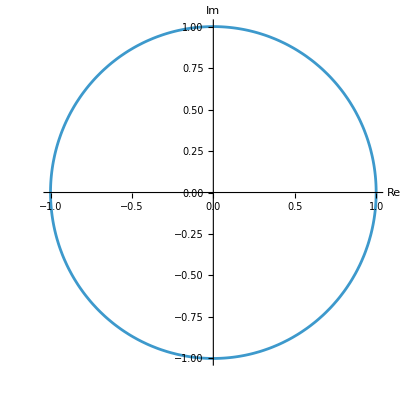

```mathematica
ParametricPlot[ReIm[E^(I ω)],{ω,0,2 π},AxesLabel->{"Re","Im"}]
```

Gráfica polar

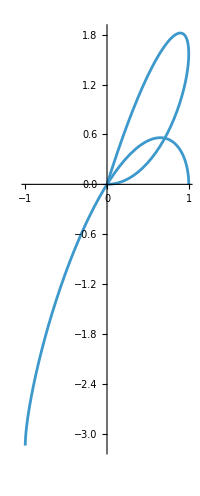

```mathematica
PolarPlot[AbsArg[E^(I ω)],{ω,0,π}]
```

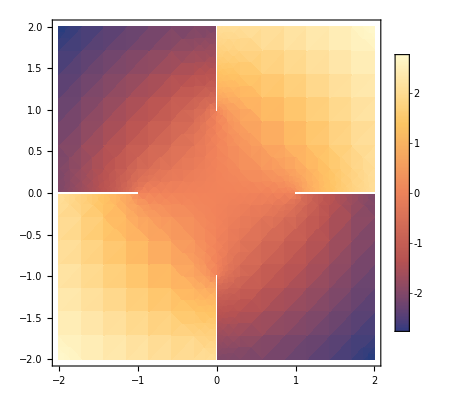

```mathematica
DensityPlot[Im[ArcSin[(x+I y)^2]],{x,-2,2},{y,-2,2},PlotLegends->Automatic]
```

## ejercicios

### 1. Grafica la superficie

z=sin(x)cos(x),  x,y∈[-3,3]

```mathematica
Plot3D[Sin[x] Cos[y],{x,-3,3},{y,-3,3}]
```

-Graphics3D-

### 2. Calcula la derivada parcial de la función:

f(x,y,z)=x^2 y+y^2 z+z^2 x

con respecto a x y z

```mathematica
D[x^2 y+ y^2 z+z^2 x,x,z]
```

2 z

```mathematica
D[(x^2 y+ y^2 z+z^2 x), x,z]
```

2 z

### 3. Resuelve la ecuación diferencial:

y''(x)+y(x)=0

con las condiciones iniciales y(0)=1 y y'(0)=0.

```mathematica
DSolveValue[{
y''[x]+y[x]==0,
y[0]==1,y'[0]==0
},y[x],x]
```

Cos[x]

```mathematica
DSolve[{y''[x]+y[x]==0,y[0]==1,y'[0]==0}]
```

{{y[x]→Cos[x]}}

### 4. Calcula el producto vectorial de los vectores:

u={1,2,3} y v={4,5,6}

```mathematica
u={1,2,3};
v={4,5,6};
```

```mathematica
Cross[u,v]
```

{-3,6,-3}

### 5. Encuentra la parte real e imaginaria del número complejo:

z=(1+i)^3

```mathematica
z=(1+I)^3
```

-2+2 ⅈ

```mathematica
{Re[z],Im[z]}
```

{-2,2}

```mathematica
ReIm[z]
```

{-2,2}

## Capítulo 5

Matrices y álgebra lineal, matemáticas discretas, probabilidad, estadística, gráficos de datos, curvas de mejor ajuste y teoría de grupos.

## 5.1. Matrices y álgebra lineal

Creación de una matriz

```mathematica
{{1,2},{3,4}}
```

{{1,2},{3,4}}

```mathematica
MatrixForm[{{1,2},{3,4}}]
```

(1 | 2
3 | 4)

```mathematica
{{1,2},{3,4}} //MatrixForm
```

(1 | 2
3 | 4)

Producto de matrices

```mathematica
Clear[{a,b,c,d}]
```

```mathematica
{{1,2},{3,4}}//MatrixForm
{{a,b},{c,d}} //MatrixForm

{{1,2},{3,4}}.{{a,b},{c,d}} //MatrixForm
```

(1 | 2
3 | 4)

(a | b
c | d)

(a+2 c | b+2 d
3 a+4 c | 3 b+4 d)

Determinante de una matriz

```mathematica
A={{a,b},{c,d}};
MatrixForm[A]
```

(a | b
c | d)

```mathematica
Det[{{a,b},{c,d}}]
Det[A]
```

-b c+a d

-b c+a d

Inversa de una matriz

```mathematica
Inverse[{{1,1},{0,1}}]
```

{{1,-1},{0,1}}

Resolución de un sistema lineal

```mathematica
A={{1,1},{0,1}};
MatrixForm[A]

LinearSolve[A,{x,y}]
```

(1 | 1
0 | 1)

{x-y,y}

## 5.2. Matemáticas discretas

Factorización de un número

```mathematica
FactorInteger[30]
```

{{2,1},{3,1},{5,1}}

```mathematica
FactorInteger[60]
```

{{2,2},{3,1},{5,1}}

Máximo común divisor (GCD)

```mathematica
GCD[24,60]
```

12

Prueba de primalidad

```mathematica
PrimeQ[7]
```

True

```mathematica
CoprimeQ[31,15] (*dos o más números enteros que no tienen factores primos en común,excepto el número 1.*)
```

True

Resto (módulo)

```mathematica
Mod[17,5]
```

2

Permutaciones de una lista

```mathematica
Permutations[{a,b,c}]
```

{{a,b,c},{a,c,b},{b,a,c},{b,c,a},{c,a,b},{c,b,a}}

Creación de un grafo

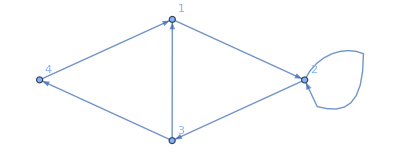

```mathematica
Graph[{
1->2,
2->3,
3->4,

4->1,
3->1,
2->2}
,VertexLabels->All]
```

Ruta más corta en un grafo

```mathematica
FindShortestPath[%,3,2]
```

{3,1,2}

## 5.3. Probabilidad

Factorial

```mathematica
5!
```

120

Combinaciones

(n
k)=(n!)/(k!(n-k)!)

(n
k)=(n
n-k)

Teorema del binomio

(a+b)^n=∑_(k=0)^n (n
k)a^(n-k)b^k

```mathematica
Binomial[4,3]
```

4

Probabilidad en una distribución binomial (dist \[Distributed])

P(X=k)=(n
k)(p^k(1-p))^(n-k)

```mathematica
n=1;
p=1/2;
k=1;
```

P(X=1)=(1
1)(1/2)^1(1-1/2)^(1-1)
P(X=1)=1•1/2(•(1/2))^0=1/2

Queremos calcular 𝑃(𝑋=1) , es decir, la probabilidad de que ocurra exactamente k=1 éxito. Tenemos que 1−p es la probabilidad de fracaso en un solo ensayo.

```mathematica
Probability[x==k,x\[Distributed]BinomialDistribution[n,p]]
```

1/2

Esperanza de una expresión (valor esperado).
𝑥 es una variable aleatoria que sigue una distribución normal estándar (NormalDistribution[]), con media 𝜇=0 y desviación estándar 𝜎=1.

La expectativa de 2 𝑥 + 3 está dada por:

E[2x+3]=2E[x]+E[3]
E[2x+3]=2(0)+(3) =3

```mathematica
Expectation[2 x+3,x\[Distributed]NormalDistribution[]]
```

3

Función de densidad de probabilidad (PDF).
La PDF se usa para determinar la probabilidad de que la variable tome valores en un rango específico

f(x)=1/(σ √(2π))e^((x-μ)^2/(2 σ^2))

Calcula la función de densidad de probabilidad de una distribución normal estándar (con media 𝜇=0 y desviación estándar 𝜎=1) en el valor 𝑥.

```mathematica
μ=0;
σ=1;
PDF[NormalDistribution[μ,σ],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

Gráfico de una PDF

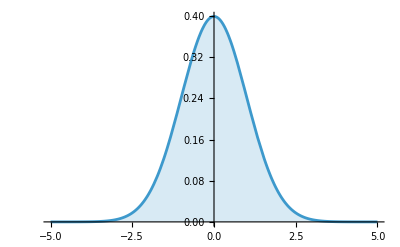

```mathematica
Plot[%,{x,-5,5},Filling->Axis]
```

## 5.4. Estadística

Media de una lista

μ=(x_1+x_2+...+x_n)/n

```mathematica
Mean[{1,2,4,5}]
```

3

Correlación entre listas

Corr(X,Y)=(Cov(X,Y))/(σ_X σ_Y)

Cov(X,Y): Covarianza entre las listas 𝑋 y 𝑌.
σ_X σ_Y: Desviaciones estándar de las listas 𝑋 y 𝑌.

```mathematica
X={1,3,5};
Y={6,4,2};
Covariance[X,Y]/(StandardDeviation[X]*StandardDeviation[Y])
```

-1

```mathematica
Correlation[X,Y]
```

-1

Desviación estándar de una distribución de Poisson
Una distribución de Poisson se caracteriza por el parámetro 𝜆 , que es el número promedio de ocurrencias en el intervalo.

P(X=k)=(λ^k e^-λ)/(k!)

k: número de eventos que queremos analizar (𝑘=0, 1, 2, …).

```mathematica
StandardDeviation[PoissonDistribution[2]]
```

√2

Calcula el momento de una lista de símbolos
Da el orden r del momento μ_r de los datos.

Moment[{𝑥1,𝑥2,…,𝑥_m},𝑛]=1/m∑_(i=1)^m x_i^n

```mathematica
Moment[{Subscript[x, 1],Subscript[x, 2]},1]
```

1/2 (x_1+x_2)

```mathematica
Moment[{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},2]
```

1/3 (x_1^2+x_2^2+x_3^2)

```mathematica
Moment[{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]},3]
```

1/3 (x_1^3+x_2^3+x_3^3)

Generación de datos aleatorios
Da un arreglo de n_1×n_2×... de variaciones pseudoaleatorias de la distribución simbólica dist.

```mathematica
RandomVariate[
NormalDistribution[0,1],
{100,2}] //Short//MatrixForm
```

{{0.211873,0.57743},«98»,{«19»,-«20»}}

```mathematica
Histogram3D[%]
```

-Graphics3D-

```mathematica
data=RandomVariate[NormalDistribution[1,3],100];
Length[data]
data
```

100

{-0.467416,3.82765,1.074,-3.47409,-2.91114,5.11977,-0.715272,2.46992,-3.85163,0.98929,2.05612,2.59656,-8.03786,4.67292,-1.79529,1.75182,-0.865168,0.694955,4.89267,-1.2288,3.63991,1.16308,3.8343,1.19554,1.4619,-3.77631,-0.685711,1.24565,-1.03354,0.972227,0.0352702,1.28576,2.55953,0.596099,3.49,3.61757,-0.633397,0.601329,-2.51326,-2.00335,4.68327,1.15452,-4.354,6.46077,1.75391,0.629801,3.97711,-0.848362,-0.429684,2.87867,0.202171,7.09808,-0.641167,2.98151,-0.895248,-2.78626,-4.98609,2.79154,4.60646,3.01076,1.73054,3.99822,-0.881538,-5.13948,0.716729,-0.274648,5.22445,-3.85374,4.17735,1.84813,0.172175,2.10477,2.83081,1.34277,2.38765,2.26493,-1.69412,4.8237,2.42801,2.04603,-5.73022,6.93319,0.00178793,1.23761,0.668332,1.25741,4.75524,2.75217,-2.08248,3.53424,5.91424,0.674185,3.88669,-1.57753,-1.62808,1.72207,-1.57247,-6.36318,4.2646,3.23528}

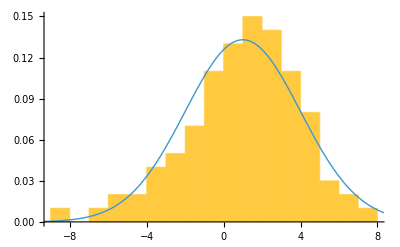

```mathematica
Show[
Histogram[data,20,"ProbabilityDensity"],
Plot[PDF[NormalDistribution[1,3],x],{x,-10,10},PlotStyle->Thick]]
```

## 5.5. Gráficos de datos y curvas de mejor ajuste

Visualización de datos y ajustar curvas

Gráfico de dispersión

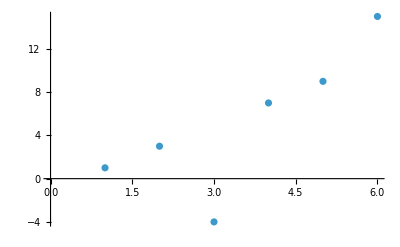

```mathematica
ListPlot[{1,3,-4,7,9,15}]
```

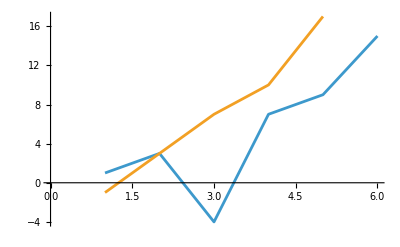

```mathematica
ListLinePlot[{{1,3,-4,7,9,15},{-1,3,7,10,17}}]
```

Diagrama de barras

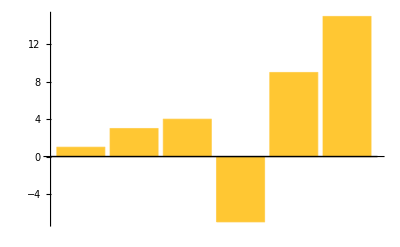

```mathematica
BarChart[{1,3,4,-7,9,15}]
```

Curva de mejor ajuste a una curva cuadrática

9.8-7.8 x+1.42857 x^2

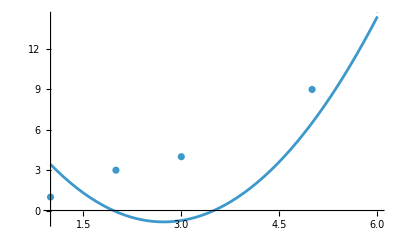

```mathematica
Fit[{1,3,4,-7,9,15},{1,x,x^2},x]

Show[{Plot[%,{x,1,6}],ListPlot[{1,3,4,-7,9,15}]}]
```

-3.2+2.15714 x+0.357143 x^2

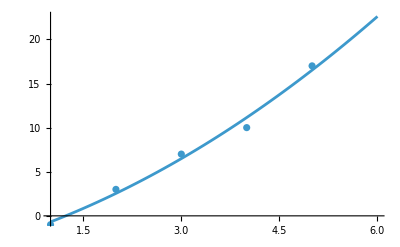

```mathematica
Fit[{-1,3,7,10,17},{1,x,x^2},x]

Show[{Plot[%,{x,1,6}],ListPlot[{-1,3,7,10,17}]}]
```

## 5.6. Teoría de grupos

Grupos y operaciones de teoría de grupos.

Elementos de un grupo simétrico

```mathematica
GroupElements[SymmetricGroup[2]]
```

{Cycles[{}],Cycles[{{1,2}}]}

Generadores de un grupo simétrico

```mathematica
GroupGenerators[SymmetricGroup[3]]
```

{Cycles[{{1,2}}],Cycles[{{1,2,3}}]}

Orden de un grupo

```mathematica
GroupOrder[PermutationGroup[{Cycles[{{3,1,2}}],Cycles[{{2,5,6}}]}]]
```

60

Tabla de multiplicación de un grupo

```mathematica
TableForm[GroupMultiplicationTable[DihedralGroup[2]],TableHeadings->Automatic]
```

| 1 | 2 | 3 | 4
1 | 1 | 2 | 3 | 4
2 | 2 | 1 | 4 | 3
3 | 3 | 4 | 1 | 2
4 | 4 | 3 | 2 | 1

Grafo de Cayley

```mathematica
CayleyGraph[DihedralGroup[2]]
```

-Graphics-

## ejercicios

### 1. Calcula el determinante de la matriz:

A=(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
A={{1,2,3},{4,5,6},{7,8,9}};
Det[A]
```

0

### 2. Encuentra todas las permutaciones de la lista :

b={1,2,3}

```mathematica
b={1,2,3};
Permutations[b]
```

{{1,2,3},{1,3,2},{2,1,3},{2,3,1},{3,1,2},{3,2,1}}

### 3. Calcula la probabilidad de que x=2 en una distribución binomial con n=5 y p=0.5.

Probabilidad en una distribución binomial (dist \[Distributed])

P(X=k)=(n
k)(p^k(1-p))^(n-k)

P(X=2)=(5
2)(1/2)^2(1-1/2)^(5-2)
P(X=2)=10•1/4(•(1/2))^3

Queremos calcular 𝑃(𝑋=1) , es decir, la probabilidad de que ocurra exactamente k=1 éxito.

```mathematica
10*1/4*(1/2)^3//N
```

0.3125

```mathematica
n=5;
p=0.5;
k=2;
Probability[x==k,x\[Distributed]BinomialDistribution[n,p]]
```

0.3125

### 4. Ajusta una curva cuadrática a los datos

{1,4,9,16,25}

1. x^2

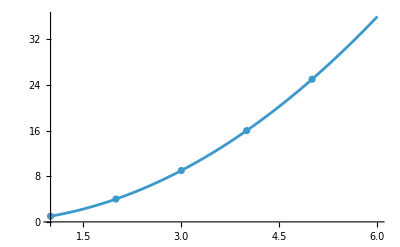

```mathematica
Fit[{1,4,9,16,25},{1,x,x^2},x]//Chop
Show[{Plot[%,{x,1,6}],ListPlot[{1,4,9,16,25}]}]
```

### 5. Encuentra el orden del grupo simétrico S_4

```mathematica
GroupOrder[SymmetricGroup[4]]
```

24